```mathematica
Zur Aufgabe 1 auf Seite 108 im Ashcroft
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
A={1/2 {1,0,1},{0,0,1},{0,1/2,1/2}};
```

```mathematica
B= Inverse[Transpose[A] ]
```

{{2,0,0},{-1,-1,1},{0,2,0}}

```mathematica
1/2(A[[1]]+A[[3]]-A[[2]]/2)
```

{1/4,1/4,1/4}

```mathematica
b=Sort[Transpose[Tally[Flatten[Table[Table[Table[Norm[h B[[1]]+k B[[2]]+l B[[3]]],{h,-5,5}],{k,-5,5}],{l,-5,5}],3]]][[1]],#1<#2&][[2;;5]]
```

{√3,2,2 √2,√11}

```mathematica
T=2 ArcSin[x/2*b]/Pi*180;
```

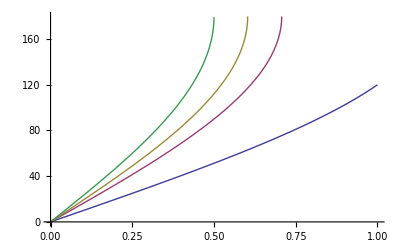

```mathematica
Plot[{T},{x,0,1}]
```

```mathematica
Solve[T[[1]]==42.8,x]
T/.%
```

{{x→0.421323}}

{{42.8,73.1453,88.6433,114.841}}

```mathematica
1.5/0.4156885081510353
```

3.60847

```mathematica
Sort[Transpose[Tally[Flatten[Table[Table[Table[ {Abs[1+Exp[I Pi /2 (h+l-k 2)]],Norm[h B[[1]]+k B[[2]]+l B[[3]]]},{h,-5,5}],{k,-5,5}],{l,-5,5}],2]]][[1]],#1[[2]]<#2[[2]]&]
```

{{2,0},{0,√3},{√2,√3},{2,√3},{√2,2},{0,2},{2,2 √2},{0,2 √2},{√2,2 √2},{2,√11},{√2,√11},{0,√11},{0,2 √3},{2,2 √3},{0,4},{2,4},{2,√19},{0,√19},{√2,√19},{2,2 √5},{√2,2 √5},{√2,2 √6},{2,2 √6},{0,2 √6},{0,3 √3},{√2,3 √3},{2,3 √3},{2,4 √2},{0,4 √2},{0,√35},{2,√35},{√2,√35},{0,6},{√2,6},{0,2 √10},{2,2 √10},{√2,2 √10},{2,√43},{√2,√43},{0,√43},{2,2 √11},{0,2 √11},{2,4 √3},{2,√51},{√2,√51},{0,√51},{√2,2 √13},{√2,2 √14},{0,2 √14},{2,2 √14},{0,√59},{2,√59},{√2,√59},{2,8},{2,√67},{√2,√67},{0,√67},{0,2 √17},{√2,2 √17},{2,6 √2},{0,6 √2},{√2,6 √2},{0,5 √3},{√2,5 √3},{2,5 √3},{0,2 √19},{2,2 √19},{2,4 √5},{0,4 √5},{2,√83},{0,√83},{√2,√83},{√2,2 √21},{2,2 √21},{2,2 √22},{0,2 √22},{2,√91},{0,√91},{√2,√91},{0,4 √6},{2,3 √11},{√2,3 √11},{0,3 √11},{√2,10},{2,2 √26},{0,2 √26},{√2,2 √26},{0,√107},{√2,√107},{2,√107},{0,6 √3},{2,6 √3},{0,√115},{√2,√115},{2,√115},{√2,2 √29},{0,2 √30},{2,2 √30},{√2,2 √30},{2,√123},{0,√123},{√2,√123},{2,8 √2},{0,√131},{2,√131},{√2,√131},{√2,2 √33},{0,2 √33},{0,2 √34},{2,2 √34},{√2,√139},{0,√139},{2,√139},{0,2 √35},{2,2 √35},{2,12},{0,7 √3},{2,7 √3},{√2,7 √3},{2,2 √37},{2,2 √38},{√2,2 √38},{0,2 √38},{2,√155},{0,√155},{√2,√155},{0,4 √10},{0,√163},{√2,√163},{2,√163},{0,2 √41},{√2,2 √41},{√2,2 √42},{√2,3 √19},{0,3 √19},{2,3 √19},{2,4 √11},{2,√179},{0,√179},{√2,√179},{√2,6 √5},{√2,2 √46},{0,√187},{2,√187},{√2,√187},{0,√195},{√2,√195},{2,√195},{√2,14},{2,10 √2},{0,10 √2},{2,√203},{√2,√203},{0,√203},{2,2 √51},{√2,√211},{√2,2 √53},{2,2 √53},{0,6 √6},{2,6 √6},{0,√219},{√2,√219},{0,4 √14},{√2,√227},{0,√227},{√2,2 √57},{√2,9 √3},{2,9 √3},{0,2 √62},{√2,2 √62},{2,2 √62},{0,√251},{2,√251},{√2,√251},{√2,√259},{0,√259},{√2,2 √65},{2,√267},{2,5 √11},{√2,5 √11},{0,5 √11},{√2,2 √69},{0,2 √73},{2,√299},{√2,√299},{2,4 √19},{2,2 √78},{√2,3 √35},{√2,√331},{2,√347},{√2,2 √89},{0,11 √3},{0,√371},{0,2 √102},{√2,√419},{2,5 √19}}

```mathematica
b={√3,2 √2,√11,4}
```

{√3,2 √2,√11,4}

{√3,2 √2,√11,√19}